```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

### Define Functions

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;

fitnew[input_,output_,len_]:=Module[{temp=Range[1,len],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]<0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000],{i,Length[hwhmi]}];,{ii,len}];output=temp;];

store[param_,res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=param/.model[[i,ii]]["BestFitParameters"],{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Snnscan/results/"<>temp<>".dat",res];];

storearea[res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=π/2(Γ/.model[[i,ii]]["BestFitParameters"])( const/.model[[i,ii]]["BestFitParameters"]),{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Snnscan/results/"<>temp<>".dat",res];];

import[res_]:=res=Import["spectraldata/Snnscan/results/"<>ToString[res]<>".dat"];
```

## Snn Scan

```mathematica
(* s here is √Subscript[s, NN] in GeV*)
T[s_]:=Tlim 1/(1+Exp[1.72-Log[s/0.45]]);
μ[s_]:=(1303 10^-3)/(1+0.286 s);
Tlim=0.155;
```

```mathematica
Tmuscan=Join[Table[{i,T[i],μ[i]},{i,8,195,10}],Table[{i,T[i],μ[i]},{i,200,1000,100}],Table[{i,T[i],μ[i]},{i,2000,10000,1000}]]
```

{{8,0.117949,0.39629},{18,0.136011,0.211939},{28,0.142234,0.144649},{38,0.145385,0.109791},{48,0.147289,0.0884709},{58,0.148563,0.0740846},{68,0.149476,0.0637226},{78,0.150162,0.0559036},{88,0.150697,0.0497936},{98,0.151125,0.0448877},{108,0.151475,0.0408618},{118,0.151768,0.0374986},{128,0.152015,0.0346469},{138,0.152228,0.0321983},{148,0.152412,0.0300729},{158,0.152573,0.0282108},{168,0.152716,0.0265658},{178,0.152842,0.0251021},{188,0.152955,0.0237913},{200,0.153077,0.0223883},{300,0.153712,0.0150115},{400,0.154032,0.0112912},{500,0.154225,0.00904861},{600,0.154354,0.00754925},{700,0.154446,0.00647614},{800,0.154515,0.00567015},{900,0.154568,0.00504257},{1000,0.154611,0.00454007},{2000,0.154805,0.002274},{3000,0.15487,0.00151688},{4000,0.154903,0.00113799},{5000,0.154922,0.000910552},{6000,0.154935,0.000758882},{7000,0.154944,0.000650524},{8000,0.154951,0.000569244},{9000,0.154957,0.000506019},{10000,0.154961,0.000455435}}

```mathematica
Do[ccdata[n]=Import["spectraldata/Snnscan/cc/swccs"<>ToString[Tmuscan[[n,1]]]<>"spectra.dat"];,{n,Length[Tmuscan]}];
Do[ccdatau[n]=Import["spectraldata/Snnscan/cc/swccs"<>ToString[Tmuscan[[n,1]]]<>"uspectra.dat"];,{n,Length[Tmuscan]}];
Do[ccdatal[n]=Import["spectraldata/Snnscan/cc/swccs"<>ToString[Tmuscan[[n,1]]]<>"lspectra.dat"];,{n,Length[Tmuscan]}];
```

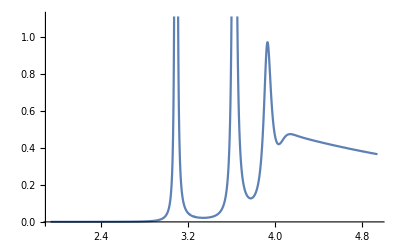

```mathematica
ListPlot[ccdatal[6],Joined->True]
```

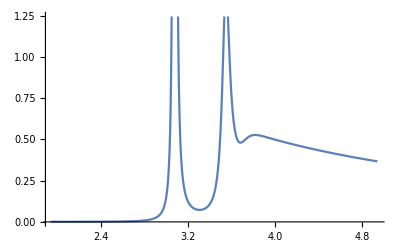

```mathematica
ListPlot[ccdata[6],Joined->True]
```

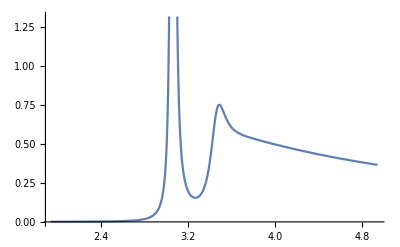

```mathematica
ListPlot[ccdatau[6],Joined->True]
```

### Perform Fitting

```mathematica
Clear[ccmodel,ccmodell,ccmodelu]
fitnew[ccdata,ccmodel,Length[Tmuscan]];
fitnew[ccdatau,ccmodelu,Length[Tmuscan]];
fitnew[ccdatal,ccmodell,Length[Tmuscan]];
```

```mathematica
Do[If[Length[ccmodel[[i]]]>2,ccmodel[[i]]=ccmodel[[i,;;2]]];,{i,Length[ccmodel]}];
Do[If[Length[ccmodelu[[i]]]>2,ccmodelu[[i]]=ccmodelu[[i,;;2]]];,{i,Length[ccmodelu]}];
Do[If[Length[ccmodell[[i]]]>2,ccmodell[[i]]=ccmodell[[i,;;2]]];,{i,Length[ccmodell]}];
```

```mathematica
Clear[wrfitcc,gfitcc,areafitcc,cfitcc,dfitcc,sfitcc,s2fitcc,wrfitccu,gfitccu,areafitccu,cfitccu,dfitccu,sfitccu,s2fitccu,wrfitccl,gfitccl,areafitccl,cfitccl,dfitccl,sfitccl,s2fitccl];
store[wr,wrfitcc,ccmodel];
store[Γ,gfitcc,ccmodel];
store[const,cfitcc,ccmodel];
store[δbg,dfitcc,ccmodel];
store[shift,sfitcc,ccmodel];
store[shift2,s2fitcc,ccmodel];
storearea[areafitcc,ccmodel];
store[wr,wrfitccu,ccmodelu];
store[Γ,gfitccu,ccmodelu];
store[const,cfitccu,ccmodelu];
store[δbg,dfitccu,ccmodelu];
store[shift,sfitccu,ccmodelu];
store[shift2,s2fitccu,ccmodelu];
storearea[areafitccu,ccmodelu];
store[wr,wrfitccl,ccmodell];
store[Γ,gfitccl,ccmodell];
store[const,cfitccl,ccmodell];
store[δbg,dfitccl,ccmodell];
store[shift,sfitccl,ccmodell];
store[shift2,s2fitccl,ccmodell];
storearea[areafitccl,ccmodell];
```

### Import previous results

```mathematica
import[wrfitcc];
import[gfitcc];
import[cfitcc];
import[dfitcc];
import[sfitcc];
import[s2fitcc];
import[areafitcc];
import[wrfitccu];
import[gfitccu];
import[cfitccu];
import[dfitccu];
import[sfitccu];
import[s2fitccu];
import[areafitccu];
import[wrfitccl];
import[gfitccl];
import[cfitccl];
import[dfitccl];
import[sfitccl];
import[s2fitccl];
import[areafitccl];
```

Import::nffil: File not found during Import.

Set::shape: Lists {{3.0658,3.47244},{3.07751,3.54466},{3.07898,3.55379},{3.07862,3.55172},{3.07798,3.54793},{3.07736,3.54426},{3.07682,3.54108},{3.07636,3.53835},{3.07597,3.53605},{3.07564,3.53407},«17»,{3.0723,3.51384},{3.07208,3.51247},{3.072,3.51201},{3.07197,3.51177},{3.07194,3.51166},{3.07193,3.51157},{3.07192,3.51149},{3.07191,3.51144},{3.0719,3.51141},{3.0719,3.51138}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.0171628,0.110676},{0.0121976,0.0734379},{0.0117421,0.0706954},{0.0122351,0.0735189},{0.012863,0.0769163},{0.0133893,0.0799477},{0.0139011,0.0825906},{0.0143115,0.0847645},{0.0146479,0.0865802},«19»,{0.0178981,0.106027},{0.0179604,0.106419},{0.0179958,0.106594},{0.0180162,0.106767},{0.0180283,0.106854},{0.0180387,0.106875},{0.0180456,0.106922},{0.0180458,0.106956},{0.0180479,0.106984}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{18.9072,0.586283},{27.4786,1.35528},{28.6629,1.48896},{27.4806,1.4082},{26.0926,1.30955},{25.024,1.22748},{24.0669,1.16178},{23.3472,1.10987},{22.7867,1.06917},{22.3526,1.03594},«17»,{18.663,0.767661},{18.4511,0.753055},{18.3833,0.748208},{18.3453,0.745689},{18.3234,0.744631},{18.3104,0.743786},{18.2992,0.742808},{18.2918,0.742356},{18.2913,0.742015},{18.289,0.741738}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.515722,0.36207},{0.515258,0.223319},{0.515332,0.219543},{0.517185,0.218294},{0.515856,0.218651},{0.517458,0.221064},{0.515319,0.223739},{0.514681,0.227197},{0.514771,0.230416},{0.515106,0.23403},«18»,{0.516052,0.282606},{0.516011,0.283878},{0.515932,0.284634},{0.515699,0.28445},{0.515953,0.284511},{0.515749,0.285156},{0.51579,0.285177},{0.515789,0.285206},{0.516062,0.285225}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.058778,0.774178},{0.0359316,0.900448},{0.0326265,0.798524},{0.0305055,0.829949},{0.0392376,0.872131},{0.035769,0.899719},{0.0444852,0.916931},{0.0420662,0.92463},{0.0405922,0.929014},{0.0445096,0.927816},«18»,{0.0557729,0.82469},{0.0572477,0.820912},{0.0559129,0.818708},{0.0580237,0.819038},{0.0556857,0.818861},{0.0572087,0.816946},{0.0566248,0.816842},{0.0580815,0.816811},{0.0559947,0.816747}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.0176239,0.273622},{0.0114945,0.165957},{0.0109374,0.14636},{0.0114832,0.15579},{0.0120812,0.168612},{0.0126328,0.179824},{0.0131699,0.189012},{0.0135679,0.196704},{0.0139139,0.202752},«19»,{0.0175206,0.247875},{0.0175955,0.248576},{0.0176372,0.249029},{0.0176638,0.248938},{0.0176707,0.249015},{0.0176878,0.249323},{0.0177123,0.249365},{0.0176984,0.249393},{0.0177199,0.249417}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.509723,0.101925},{0.526491,0.156339},{0.528672,0.165347},{0.528144,0.162623},{0.527206,0.158219},{0.526303,0.154149},{0.52552,0.150722},{0.524858,0.147777},{0.524298,0.145407},{0.523821,0.143483},«18»,{0.518738,0.125419},{0.518632,0.125072},{0.51858,0.124856},{0.518548,0.124882},{0.518528,0.124841},{0.518511,0.124702},{0.5185,0.124681},{0.518492,0.124663},{0.518483,0.124649}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{3.04919,3.38118},{3.06249,3.45334},{3.06389,3.46166},{3.06308,3.45737},{3.06199,3.45168},{3.061,3.44643},{3.06016,3.4421},{3.05945,3.43835},{3.05886,3.4353},{3.05836,3.43266},«17»,{3.05341,3.40736},{3.05309,3.40569},{3.05298,3.40513},{3.05292,3.40485},{3.05289,3.40471},{3.05287,3.40457},{3.05285,3.40453},{3.05284,3.40459},{3.05283,3.40442},{3.05283,3.40443}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.0262849,0.195355},{0.0219662,0.143973},{0.0220355,0.141293},{0.0230932,0.148584},{0.0241677,0.156436},{0.0250731,0.16322},{0.0258199,0.168805},{0.0264207,0.173365},{0.026952,0.177177},«19»,{0.0319267,0.211922},{0.0320185,0.212477},{0.0320586,0.212804},{0.0320884,0.212969},{0.0321132,0.213085},{0.032127,0.213181},{0.0321399,0.213242},{0.0321491,0.213301},{0.0321556,0.21335}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{11.7982,0.162438},{14.6436,0.404778},{14.6548,0.430763},{13.9534,0.400733},{13.2943,0.369465},{12.7804,0.343341},{12.3829,0.323482},{12.0784,0.306763},{11.8216,0.293884},{11.6306,0.282986},«17»,{9.92056,0.190381},{9.82693,0.184687},{9.79604,0.182672},{9.78231,0.181774},{9.77239,0.18134},{9.76425,0.180773},{9.75968,0.180771},{9.75545,0.181397},{9.75242,0.180442},{9.75027,0.180579}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.522196,0.40145},{0.515327,0.383248},{0.514903,0.376137},{0.514817,0.374902},{0.514937,0.373728},{0.51515,0.37371},{0.515518,0.372901},{0.515887,0.373321},{0.515558,0.372973},{0.516412,0.373099},«18»,{0.516521,0.369433},{0.51661,0.36935},{0.516693,0.36936},{0.516666,0.369199},{0.516565,0.369302},{0.516525,0.369103},{0.516459,0.368489},{0.516461,0.369075},{0.51644,0.368887}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.11778,0.273785},{0.079245,0.520008},{0.0778583,0.531542},{0.0828701,0.499634},{0.088134,0.468643},{0.0925599,0.439942},{0.0963467,0.418738},{0.10036,0.398429},{0.103309,0.383313},{0.105247,0.369612},«18»,{0.132009,0.240103},{0.13192,0.237458},{0.132633,0.236044},{0.132683,0.235686},{0.132758,0.23471},{0.132927,0.234937},{0.13314,0.23661},{0.13308,0.234456},{0.133265,0.23486}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.0308934,0.354281},{0.0231017,0.297414},{0.0229345,0.293559},{0.0241797,0.297997},{0.02552,0.303058},{0.0266722,0.307945},{0.0276541,0.31192},{0.0284975,0.315754},{0.0291986,0.318791},«19»,{0.0361859,0.353127},{0.0362869,0.353954},{0.0363771,0.354299},{0.036415,0.354468},{0.036447,0.354719},{0.036463,0.354694},{0.0364761,0.354384},{0.0364908,0.354829},{0.0365017,0.354749}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.487125,0.0498462},{0.505269,0.0915416},{0.507251,0.0956043},{0.506154,0.0935295},{0.504686,0.0907883},{0.503353,0.0880275},{0.502222,0.085774},{0.501274,0.0835382},{0.50048,0.0817906},{0.499815,0.0801587},«18»,{0.492824,0.0614801},{0.492687,0.0609683},{0.492613,0.0607618},{0.49257,0.0606637},{0.492541,0.0605073},{0.492521,0.0605337},{0.492506,0.060761},{0.492494,0.0604575},{0.492484,0.0605172}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{3.07966,3.5572},{3.08914,3.61941},{3.09043,3.62844},{3.09038,3.62813},{3.0901,3.62612},{3.08979,3.62397},{3.08951,3.62202},{3.08927,3.62034},{3.08906,3.61889},{3.08888,3.61764},«17»,{3.08697,3.60477},{3.08684,3.60391},{3.0868,3.60362},{3.08678,3.60348},{3.08677,3.60339},{3.08676,3.60333},{3.08675,3.60329},{3.08675,3.60326},{3.08674,3.60323},{3.08674,3.60322}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.00930622,0.0571085},{0.00452577,0.0274314},{0.00383713,0.0234952},{0.00394559,0.0241944},{0.00416395,0.0256619},{0.00441926,0.0271894},{0.00468103,0.0285656},{0.00486782,0.029716},{0.00510201,0.0307765},«19»,{0.00682337,0.0414186},{0.00685363,0.0416334},{0.00686289,0.041734},{0.00688449,0.04181},{0.00691054,0.0418636},{0.00696562,0.0419398},{0.00698615,0.0419761},{0.0069947,0.0419993},{0.00699946,0.042021}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{36.2315,1.9112},{76.5629,5.15975},{90.655,6.20603},{88.1502,6.02072},{83.4545,5.63964},{78.5619,5.28548},{74.1069,4.99862},{71.2109,4.77826},{67.9,4.59126},{66.0901,4.44527},«17»,{50.8336,3.29377},{50.4419,3.23709},{50.2129,3.21703},{50.1422,3.20738},{49.9831,3.20073},{49.7938,3.19578},{49.3989,3.18945},{49.2526,3.18634},{49.1918,3.18429},{49.1581,3.1824}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.518014,0.2304},{0.52455,0.209859},{0.52612,0.206053},{0.528277,0.206249},{0.540383,0.207236},{0.533447,0.207908},{0.527726,0.208594},{0.528485,0.209246},{0.520341,0.209298},{0.522617,0.2099},«18»,{0.527444,0.215813},{0.527585,0.215934},{0.5267,0.216024},{0.525954,0.216099},{0.525442,0.215962},{0.520721,0.215609},{0.51952,0.215518},{0.516258,0.215502},{0.51835,0.215508}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.0302612,0.678219},{0.0468029,0.107445},{0.184861,0.0803964},{0.100336,0.0830314},{-0.12408,0.0906475},{0.0456476,0.10016},{0.0345974,0.107444},{0.0410893,0.115231},{0.0356913,0.122121},«19»,{-0.0178541,0.212137},{-0.0165864,0.214061},{0.0335687,0.216159},{0.0199707,0.215339},{0.0269853,0.216647},{0.00279169,0.217167},{-0.0179737,0.217592},{0.0693013,0.217836},{-0.000582601,0.217959}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.00866502,0.1118},{0.00435601,0.027303},{0.00292568,0.0218353},{0.0033374,0.0225685},{0.00394633,0.0243176},{0.00392153,0.0261898},{0.00430953,0.027955},{0.00447098,0.0295056},{0.00462743,0.0309563},«19»,{0.00620707,0.0479999},{0.00624324,0.0483561},{0.00616666,0.0486349},{0.00614179,0.0486632},{0.00610896,0.0488431},{0.00611028,0.0489367},{0.00624834,0.0489807},{0.00627008,0.0490196},{0.00618583,0.0490566}} and $Failed are not the same shape.

Import::nffil: File not found during Import.

Set::shape: Lists {{0.529639,0.171446},{0.54429,0.222329},{0.54641,0.229041},{0.546331,0.228814},{0.545853,0.227331},{0.545358,0.225738},{0.544903,0.224292},{0.544504,0.223038},{0.544166,0.221958},{0.543875,0.221031},«18»,{0.540642,0.210606},{0.540574,0.210386},{0.540543,0.210262},{0.540524,0.210208},{0.540514,0.210152},{0.540501,0.210117},{0.540489,0.210094},{0.540483,0.210075},{0.540481,0.210059}} and $Failed are not the same shape.

### View results

```mathematica
Manipulate[Show[{ListPlot[ccdata[i],Joined->True],Plot[BW[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],dfitcc[[i,ii]],cfitcc[[i,ii]],sfitcc[[i,ii]],s2fitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],cfitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitcc],1},{ii,1,Length[wrfitcc[[1]]],1}]
```

```mathematica
Manipulate[Show[{ListPlot[ccdatau[i],Joined->True],Plot[BW[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],dfitccu[[i,ii]],cfitccu[[i,ii]],sfitccu[[i,ii]],s2fitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],cfitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitccu],1},{ii,1,Length[wrfitccu[[1]]],1}]
```

```mathematica
Manipulate[Show[{ListPlot[ccdatal[i],Joined->True],Plot[BW[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],dfitccl[[i,ii]],cfitccl[[i,ii]],sfitccl[[i,ii]],s2fitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],cfitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitccl],1},{ii,1,Length[wrfitccl[[1]]],1}]
```

### DiLetpon Ratio

```mathematica
Emfactor=2.356305815440891;
nB[w_,T_]:=1/(Exp[w/T]-1);
```

```mathematica
R0=ConstantArray[0,Length[wrfitcc]];
Do[If[Length[wrfitcc[[ii]]]==2,R0[[ii]]={Tmuscan[[ii,1]],Emfactor (areafitcc[[ii,2]]nB[wrfitcc[[ii,2]],Tmuscan[[ii,2]]])/(areafitcc[[ii,1]]nB[wrfitcc[[ii,1]],Tmuscan[[ii,2]]])}],{ii,Length[R0]}];
R0u=ConstantArray[0,Length[wrfitccu]];
Do[If[Length[wrfitccu[[ii]]]==2,R0u[[ii]]={Tmuscan[[ii,1]],Emfactor (areafitccu[[ii,2]]nB[wrfitccu[[ii,2]],Tmuscan[[ii,2]]])/(areafitccu[[ii,1]]nB[wrfitccu[[ii,1]],Tmuscan[[ii,2]]])}],{ii,Length[R0u]}];
R0l=ConstantArray[0,Length[wrfitccl]];
Do[If[Length[wrfitccl[[ii]]]==2,R0l[[ii]]={Tmuscan[[ii,1]],Emfactor (areafitccl[[ii,2]]nB[wrfitccl[[ii,2]],Tmuscan[[ii,2]]])/(areafitccl[[ii,1]]nB[wrfitccl[[ii,1]],Tmuscan[[ii,2]]])}],{ii,Length[R0l]}];
```

```mathematica
R0=DeleteCases[R0,0];
R0u=DeleteCases[R0u,0];
R0l=DeleteCases[R0l,0];
```

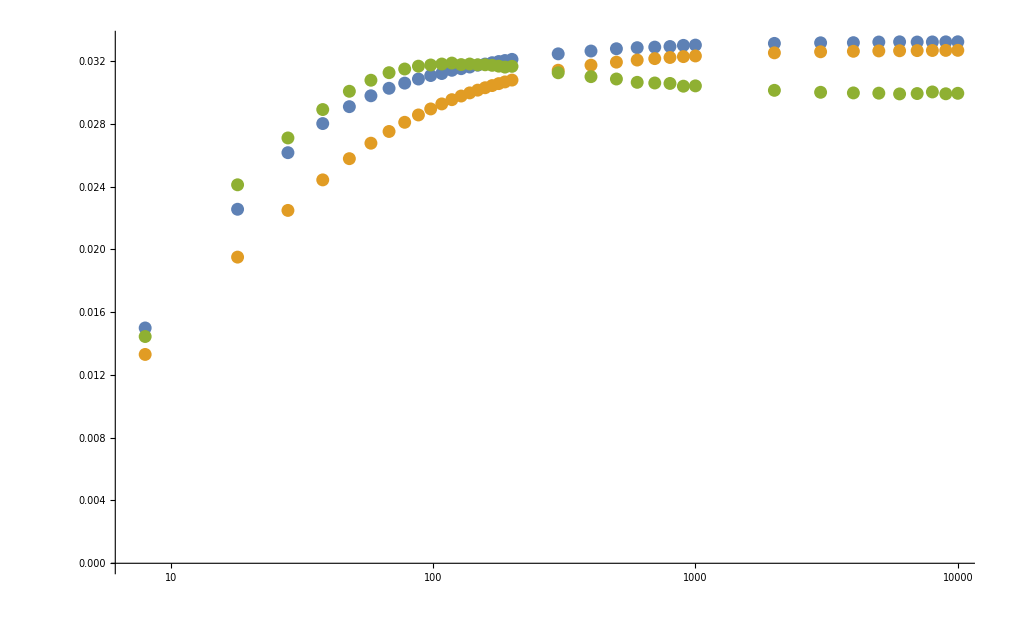

```mathematica
ListLogLinearPlot[{R0,R0l,R0u},PlotRange->All]
```

```mathematica
.
```

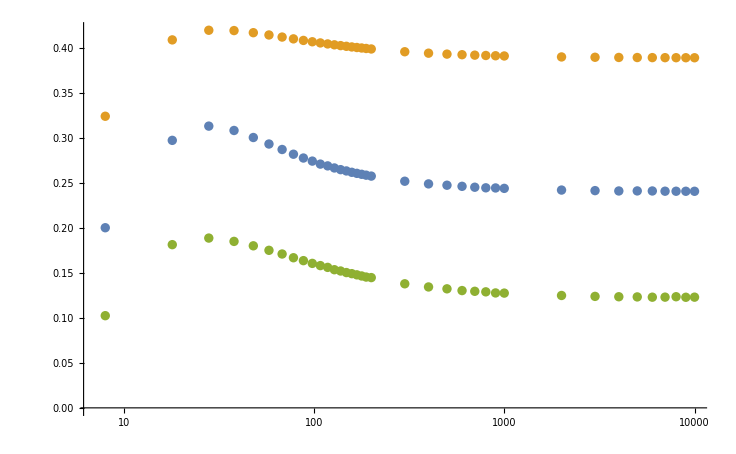

```mathematica
ListLogLinearPlot[{Table[{Tmuscan[[ii,1]],areafitcc[[ii,2]]/areafitcc[[ii,1]]},{ii,1,Length[areafitccu]}],Table[{Tmuscan[[ii,1]],areafitccl[[ii,2]]/areafitccl[[ii,1]]},{ii,1,Length[areafitccl]}],Table[{Tmuscan[[ii,1]],areafitccu[[ii,2]]/areafitccu[[ii,1]]},{ii,1,Length[areafitccu]}]},PlotRange->All]
```

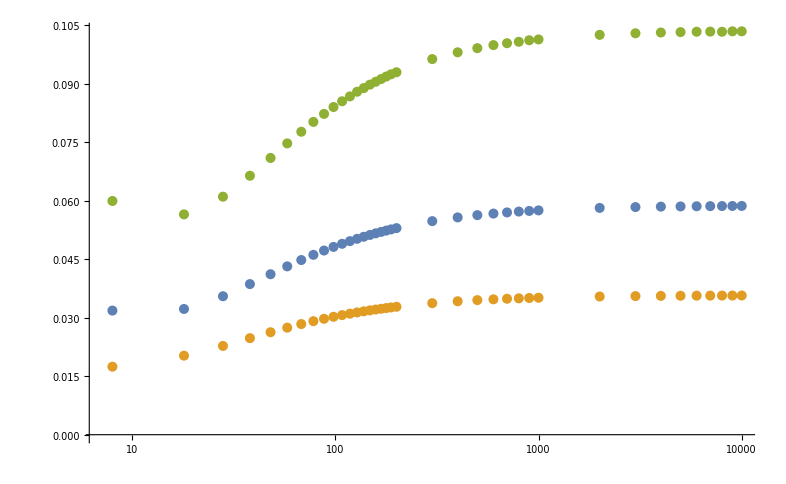

```mathematica
ListLogLinearPlot[{Table[{Tmuscan[[ii,1]],nB[wrfitcc[[ii,2]],Tmuscan[[ii,2]]]/nB[wrfitcc[[ii,1]],Tmuscan[[ii,2]]]},{ii,1,Length[areafitccu]}],Table[{Tmuscan[[ii,1]],nB[wrfitccl[[ii,2]],Tmuscan[[ii,2]]]/nB[wrfitccl[[ii,1]],Tmuscan[[ii,2]]]},{ii,1,Length[areafitccu]}],Table[{Tmuscan[[ii,1]],nB[wrfitccu[[ii,2]],Tmuscan[[ii,2]]]/nB[wrfitccu[[ii,1]],Tmuscan[[ii,2]]]},{ii,1,Length[areafitccl]}]},PlotRange->All]
```

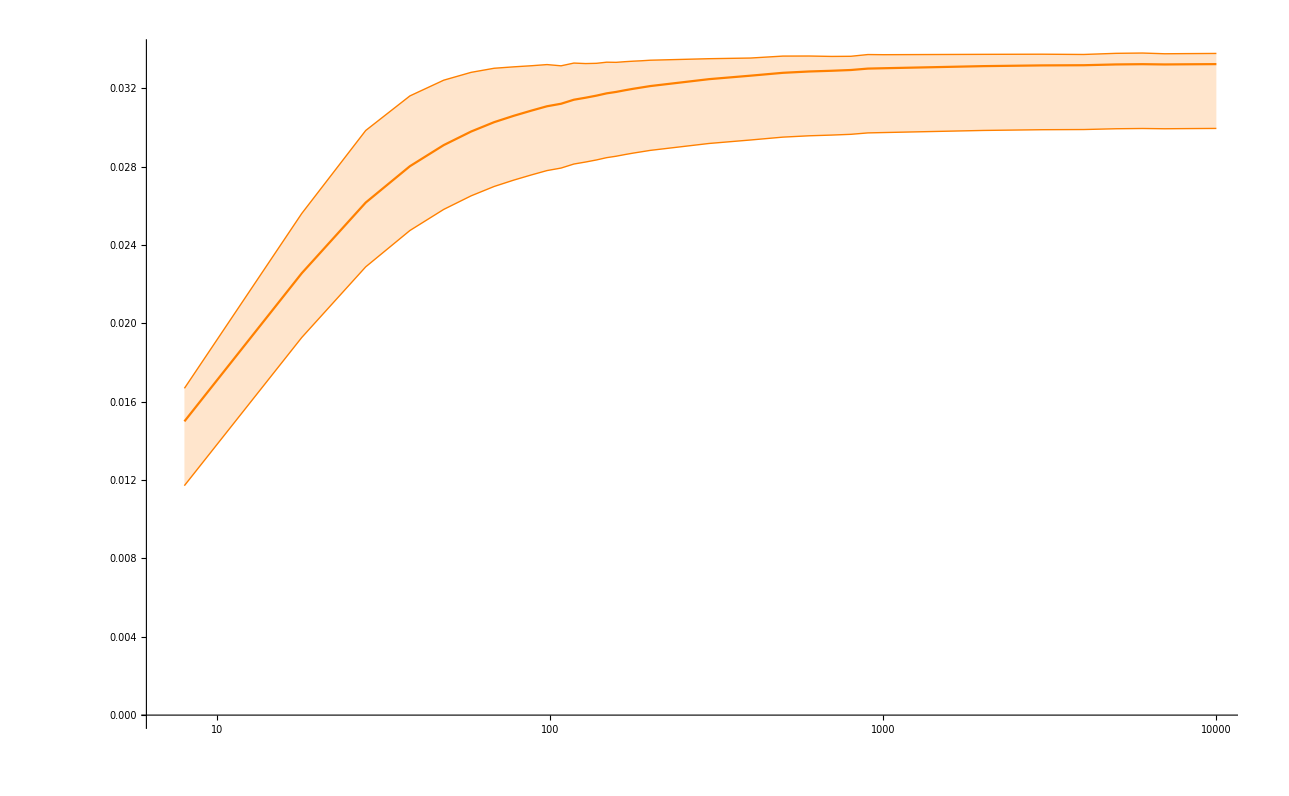

```mathematica
ListLogLinearPlot[{R0,R0-(R0[[-1,2]]-R0u[[-1,2]]),R0+(R0-R0l),R0,R0l,R0u},PlotRange->All,Joined->True,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2],PlotStyle->{Orange,{Orange,Thin},{Orange,Thin}}]
```

```mathematica
R0u[[-1,2]]
```

0.0299451

```mathematica
R0[[-1,2]]
```

0.0332278

```mathematica
R0l[[-1]]
```

{10000,0.0326827}